bendDNA[contLength_Integer,protPos_List,protRot_]: A linear molecule of DNA has length contLength. It binds with protamine at positions specified by protPos. Each protamine is assumed to bend the DNA by the angle protRot. This function computes the bent DNA geometry and plots it if plotQ is True. It also returns the loop circumference and loop start site if the DNA is single-looped.

```mathematica
bendDNA[contLength_,protPos_,protRot_,plotQ_]:=
Module[
{
segLengths,
compDisps,
compPts,

realPts,
dnaSegs,

ptsPerGroup,
dnaSegGroups,

possCross,
allCrossPts,
crossPt,

segCrossQ,

brokeSegs,
crossPos,
dnaRegions,

regionLengths,
startSite,
loopCirc
},

(*Computes the complex coordinates of each DNA bending vertex*)
segLengths=Differences[Flatten[{0,protPos,contLength}]];
compDisps=FoldList[#1/Norm[#1]*E^(I protRot)*#2&,segLengths];
compPts=Join[{0},Accumulate[compDisps]];

(*Converts to real coordinates and computes individual DNA segments*)
realPts={Re[#],Im[#]}&/@compPts;
dnaSegs=Line/@Partition[realPts,2,1];

(*Joins individual DNA segments into non-self-intersecting curves*)
ptsPerGroup=Floor[N[Pi/protRot+2]];
dnaSegGroups=Line/@Partition[realPts,UpTo[ptsPerGroup],ptsPerGroup-1];

(*Determines the DNA crossover point*)
possCross=Subsets[dnaSegGroups,{2}];
allCrossPts=Partition[Flatten[List@@#&/@Select[RegionIntersection@@#&/@possCross,!Head[#]===EmptyRegion&]],2];
crossPt=Flatten[Complement[allCrossPts,realPts]];

If[
Length[crossPt]==2,

(*Determines which DNA segments form the crossover point*)
segCrossQ=RegionMember[#,crossPt]&/@dnaSegs;

(*Determines which DNA segments belong to which region of the DNA*)
brokeSegs=Flatten[If[!#⟦2⟧,#⟦1⟧,{ReplacePart[#⟦1⟧,{1,2}->crossPt],ReplacePart[#⟦1⟧,{1,1}->crossPt]}]&/@Transpose[{dnaSegs,segCrossQ}]];
crossPos=Flatten[Position[segCrossQ,True]];
dnaRegions=TakeList[brokeSegs,{First[crossPos],Last[crossPos]-First[crossPos]+1,All}];

(*Computes the loop circumference and loop start site*)
regionLengths=Total/@ArcLength[dnaRegions];
loopCirc=regionLengths⟦2⟧;
startSite=Min[First[regionLengths],Last[regionLengths]];

(*Computation Summary*)
If[plotQ,Print[Graphics[Flatten/@Transpose[{{Red,Green,Blue},dnaRegions}],Axes->True,AxesStyle->Dashed,ImageSize->Medium]]];
Return[{loopCirc,startSite}],

If[plotQ,Print[ListPlot[realPts,Joined->True,AxesStyle->Dashed,ImageSize->Medium]]];
Return[{-1,-1}]
]
]
```

```mathematica
simulateDNABending[numTrials_,numPlots_,numProtamine_,contLength_,modelType_,protRot_]:=
Module[
{
protPos,

results,
circs,
startSites
},

results=Transpose[
Reap[
Do[
protPos=Which[
modelType=="Random",Sort[RandomReal[{0,contLength},numProtamine]],
modelType=="Electrostatic",Sort[RandomVariate[BetaDistribution[2,2],numProtamine]]
];
Sow[bendDNA[contLength,protPos,protRot,If[Mod[trial,Floor[numTrials/numPlots]]==0,True,False]]],
{trial,numTrials}
]
]⟦2⟧⟦1⟧
];

results=Select[#,#≠-1&]&/@results;

circs=results⟦1⟧;
startSites=results⟦2⟧;

Print[Histogram[circs,{0.05},"Probability",PlotLabel->"Distribution of Loop Circumferences",ImageSize->Large]];
Print[Histogram[startSites,{0.05},"Probability",PlotLabel->"Distribution of Loop Start Sites",AxesLabel->{"Fractional Loop Start Site","Probability"},ImageSize->Large]];
]
```

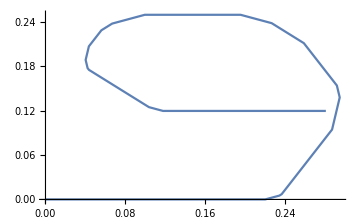

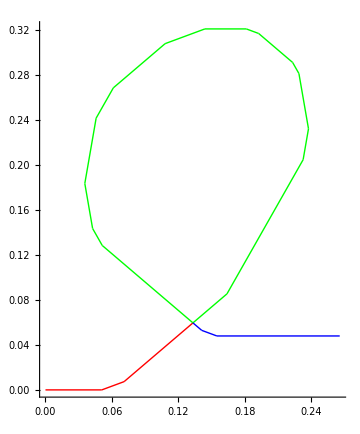

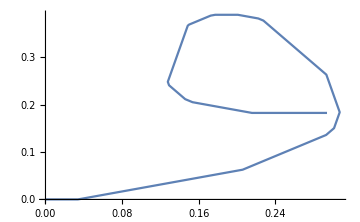

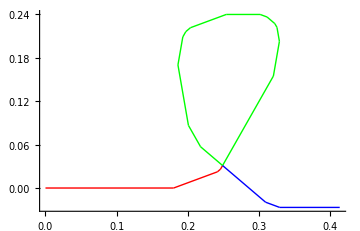

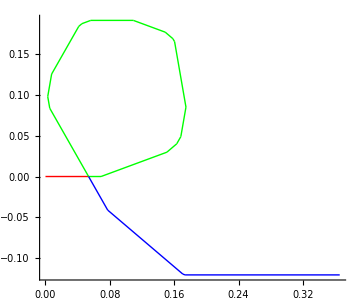

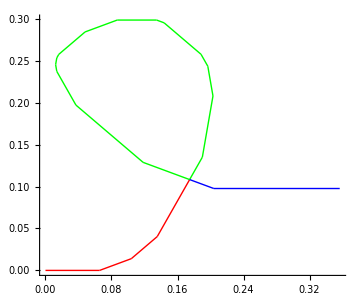

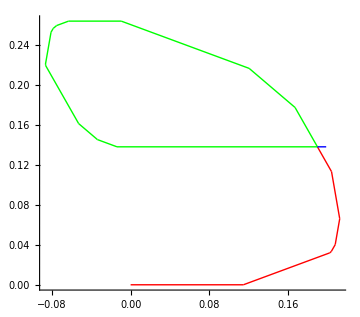

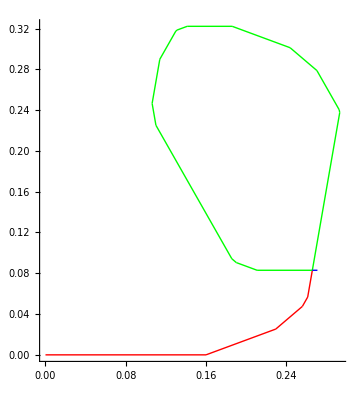

```mathematica
simulateDNABending[1000(*numTrials*),20(*numPlots*),18(*numProtamine*),1(*contLength*),"Electrostatic"(*modelType*),20Degree(*protRot*)]
```